# Q2

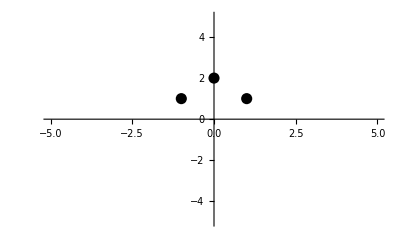

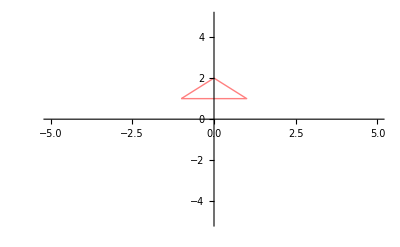

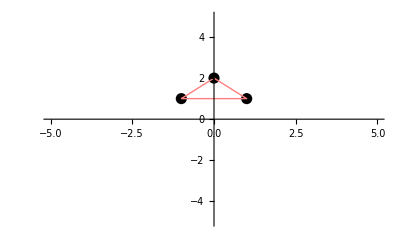

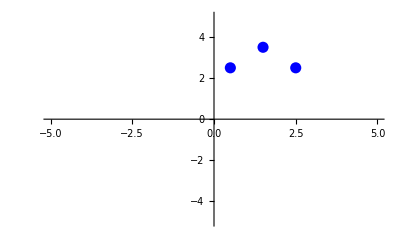

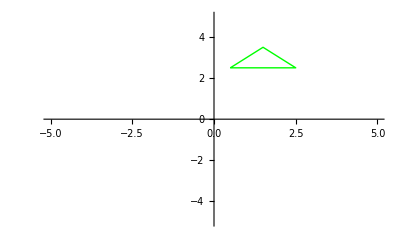

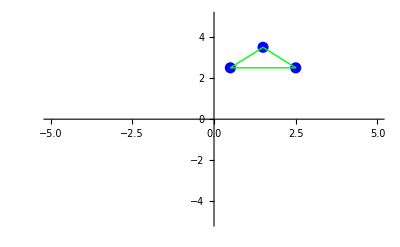

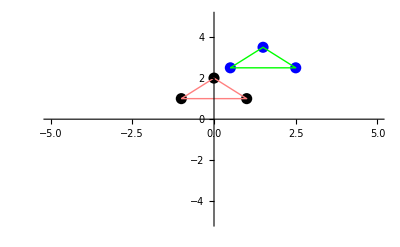

SetDelayed::write: Tag Graphics in ()[x_,y_] is Protected.

$Failed

(-Graphics-)[-1,1]

```mathematica
a={-1,1};
b={1,1};
c={0,2};
(*a*)
p1=ListPlot[
{a,b,c},
PlotStyle->{
Black,
PointSize[0.02]
},
PlotRange->{{-5,5},{-5,5}}
]
t1=ListLinePlot[
{a,b,c,a},
PlotStyle->{
Pink,
Thick
},
PlotRange->{{-5,5},{-5,5}}
]
g1=Show[p1,t1]
(*b*)
t[x_,y_]:={x+1.5,y+1.5}
t[a[[1]],a[[2]]];
t[b[[1]],b[[2]]];
t[c[[1]],c[[2]]];
p2=ListPlot[
{
t[a[[1]],a[[2]]],
t[b[[1]],b[[2]]],
t[c[[1]],c[[2]]]
},
PlotStyle->{
Blue,
PointSize[0.02]
},
PlotRange->{{-5,5},{-5,5}}
]
t2=ListLinePlot[
{
t[a[[1]],a[[2]]],
t[b[[1]],b[[2]]],
t[c[[1]],c[[2]]],
t[a[[1]],a[[2]]]
},
PlotStyle->{
Green,
Thick
},
PlotRange->{{-5,5},{-5,5}}
]
g2=Show[p2,t2]
(*c*)
Show[g1,g2]
```

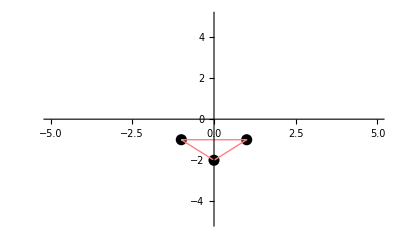

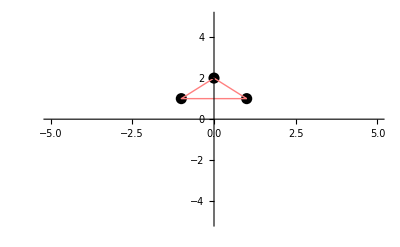

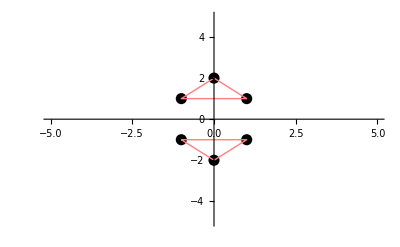

{-1,-1}

{-1,1}

{-2,0}

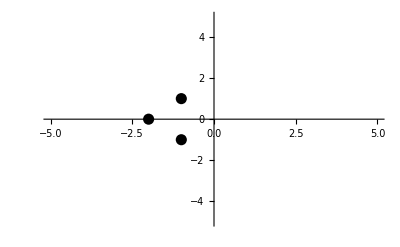

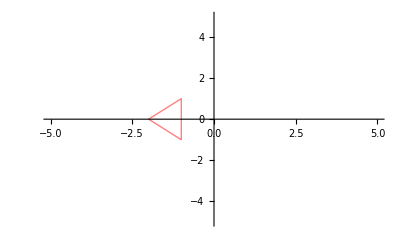

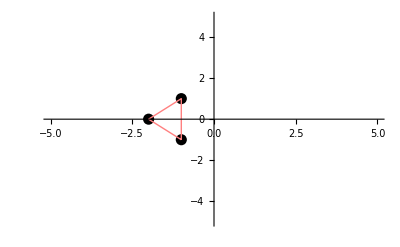

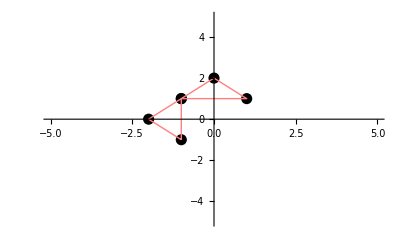

```mathematica
a={-1,1};
b={1,1};
c={0,2};
T[{x_,y_}]={x,-y};
T[a];
T[b];
T[c];
p3=ListPlot[
{
T[a],
T[b],
T[c]
},
PlotStyle->{
Black,
PointSize[0.02]
},
PlotRange->{{-5,5},{-5,5}}
];
t3=ListLinePlot[
{
T[a],
T[b],
T[c],
T[a]
},
PlotStyle->{
Pink,
Thick
},
PlotRange->{{-5,5},{-5,5}}
];
g3=Show[p3,t3]
P[{x_,y_}]={-x,y};
P[a];
P[b];
P[c];
p4=ListPlot[
{
P[a],
P[b],
P[c]
},
PlotStyle->{
Black,
PointSize[0.02]
},
PlotRange->{{-5,5},{-5,5}}
];
t4=ListLinePlot[
{
P[a],
P[b],
P[c],
P[a]
},
PlotStyle->{
Pink,
Thick
},
PlotRange->{{-5,5},{-5,5}}
];
g4 = Show[p4,t4]
Show[g3,g4]
(*e*)
r=RotationTransform[90°];
r[{x,y}];
r[a]
r[b]
r[c]
p5=ListPlot[
{
r[a],
r[b],
r[c]
},
PlotStyle->{
Black,
PointSize[0.02]
},
PlotRange->{{-5,5},{-5,5}}
]
t5=ListLinePlot[
{
r[a],
r[b],
r[c],
r[a]
},
PlotStyle->{
Pink,
Thick
},
PlotRange->{{-5,5},{-5,5}}
]
g5 = Show[p5,t5]
Show[g1,g5]
```